```mathematica
LaserDriftPlot[driftCSV_,trial_,hue_]:= Module[{driftData=driftCSV,run=trial,color=hue},
data=Drop[Import[driftData,{"Data",All,{1,2}}],{1,3}];
ListPlot[data,PlotLabels->{run}, PlotStyle->color ,AxesLabel->{"Time(s)","Frequency Change (GHz)"}]]

LaserDriftSlope[driftCSV_,trial_,hue_]:=Module[{driftData=driftCSV,run=trial,color=hue},file= Import[driftData,{"Data",All,{1,2}}];
filedata=Drop[file,{1,6}];
lm=LinearModelFit[filedata,x,x];
Show[ListPlot[filedata,PlotLabels->{run}, PlotStyle->color ,AxesLabel->{"Time(s)","Frequency Change (GHz)"}],Plot[lm["BestFit"],{x,0,2500}]]]

LaserDriftSlope["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-23trial9TOF.csv","TOF 1",Pink]

lm["ParameterTable"]

LaserDriftSlope["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial10TOF.csv","TOF 2",Green]

lm["ParameterTable"]

LaserDriftSlope["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial7.csv","SOF Trial 7",Pink]

lm["ParameterTable"]

LaserDriftSlope["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv","No Locking",Blue]

lm["ParameterTable"]
lm["Best Fit"]

LaserDriftSlope["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial11TOF.csv","TOF 3",Blue]

lm["ParameterTable"]
```

Import::nffil: File /Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-23trial9TOF.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,6}].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,6}] is not a list of numbers or pairs of numbers.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{TOF 1},PlotStyle→RGBColor[1, 0.5, 0.5],AxesLabel→{Time(s),Frequency Change (GHz)}],].

Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{TOF 1},PlotStyle→RGBColor[1, 0.5, 0.5],AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Drop[$Failed,{1,6}],x,x][ParameterTable]

Import::nffil: File /Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial10TOF.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,6}].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,6}] is not a list of numbers or pairs of numbers.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{TOF 2},PlotStyle→RGBColor[0, 1, 0],AxesLabel→{Time(s),Frequency Change (GHz)}],].

Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{TOF 2},PlotStyle→RGBColor[0, 1, 0],AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Drop[$Failed,{1,6}],x,x][ParameterTable]

Import::nffil: File /Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial7.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,6}].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,6}] is not a list of numbers or pairs of numbers.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{SOF Trial 7},PlotStyle→RGBColor[1, 0.5, 0.5],AxesLabel→{Time(s),Frequency Change (GHz)}],].

Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{SOF Trial 7},PlotStyle→RGBColor[1, 0.5, 0.5],AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Drop[$Failed,{1,6}],x,x][ParameterTable]

Import::nffil: File /Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,6}].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,6}] is not a list of numbers or pairs of numbers.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{No Locking},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],].

Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{No Locking},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Drop[$Failed,{1,6}],x,x][ParameterTable]

LinearModelFit[Drop[$Failed,{1,6}],x,x][Best Fit]

Import::nffil: File /Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial11TOF.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,6}].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,6}] is not a list of numbers or pairs of numbers.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{TOF 3},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],].

Show[ListPlot[Drop[$Failed,{1,6}],PlotLabels→{TOF 3},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Drop[$Failed,{1,6}],x,x][ParameterTable]

```mathematica
Export["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/TOF2LowPower.png",%1003,"PNG"]
```

/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/TOF2LowPower.png

```mathematica
Export["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/noLockDriftgraph.png",%995,"PNG"]
```

/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/noLockDriftgraph.png

```mathematica
Trial2=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trail2.csv","Lock Trial 2",Red];
```

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trail2.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,3}].

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,3}] is not a list of numbers or pairs of numbers.

```mathematica
NoLocking=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv","No Locking",Blue]
```

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,3}].

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,3}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[$Failed,{1,3}],PlotLabels→{No Locking},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}]

```mathematica
TrialTOF1=LaserDriftPlot["/Users/charlottezehnder/Documents/laserStabilization/Data/FrequencyDrift/FrequencyDrift2021-07-23trial9TOF.csv","TOF Trial 1" ]
```

-Graphics-

```mathematica
TrialTOF2=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial10TOF.csv","Trial TOF low Power",Green]

Trial7=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial7.csv","Trial 7",Purple];
Trial6=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial6.csv","Trial 6",Yellow];

Trial5=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial5.csv","Trial 5",Orange];
```

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial10TOF.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,3}].

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,3}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial TOF low Power},PlotStyle→RGBColor[0, 1, 0],AxesLabel→{Time(s),Frequency Change (GHz)}]

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial7.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,3}].

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,3}] is not a list of numbers or pairs of numbers.

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial6.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,3}].

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,3}] is not a list of numbers or pairs of numbers.

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial5.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,3}].

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,3}] is not a list of numbers or pairs of numbers.

```mathematica
Show[NoLocking,TrialTOF1,ImageSize->Large,PlotRange->{{0,1500},{-0.040,0.006}}]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[ListPlot[Drop[$Failed,{1,3}],PlotLabels→{No Locking},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],ListPlot[Drop[$Failed,{1,3}],PlotLabels→{TOF Trial 1},PlotStyle→RGBColor[1, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],ImageSize→Large,PlotRange→{{0,1500},{-0.04,0.006}}]

```mathematica
Export["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Photos/Laser Drift File.svg",%943,"SVG"]
```

/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Photos/Laser Drift File.svg

```mathematica
Comparison=Show[Trial2,NoLocking,Trial4,Trial3,Trial5,Trial7, PlotRange->{{0,2500},{-0.010,0.030}},ImageSize->Large,PlotLabel->"LaserDrift"]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Lock Trial 2},PlotStyle→RGBColor[1, 0, 0],AxesLabel→{Time(s),Frequency Change (GHz)}],ListPlot[Drop[$Failed,{1,3}],PlotLabels→{No Locking},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],Trial4,Trial3,ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial 5},PlotStyle→RGBColor[1, 0.5, 0],AxesLabel→{Time(s),Frequency Change (GHz)}],ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial 7},PlotStyle→RGBColor[0.5, 0, 0.5],AxesLabel→{Time(s),Frequency Change (GHz)}],PlotRange→{{0,2500},{-0.01,0.03}},ImageSize→Large,PlotLabel→LaserDrift]

```mathematica
Show[Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-ListPlot[Drop[$Failed,{1,3}],PlotLabels->{"Trial 4"},PlotStyle->RGBColor[1, 0.5, 0],AxesLabel->{"Time(s)","Frequency Change (GHz)"}],PlotRange->{{0,100},{-0.01,0.006}},ImageSize->Large,PlotLabel->"LaserDrift"],ImageSize->Tiny]
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,3}].

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,3}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Show::gtype: Show is not a type of graphics.

Show[Show[-Graphics-,-Graphics-,-Graphics-,-Graphics- ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial 4},PlotStyle→RGBColor[1, 0.5, 0],AxesLabel→{Time(s),Frequency Change (GHz)}],PlotRange→{{0,100},{-0.01,0.006}},ImageSize→Large,PlotLabel→LaserDrift],ImageSize→Tiny]

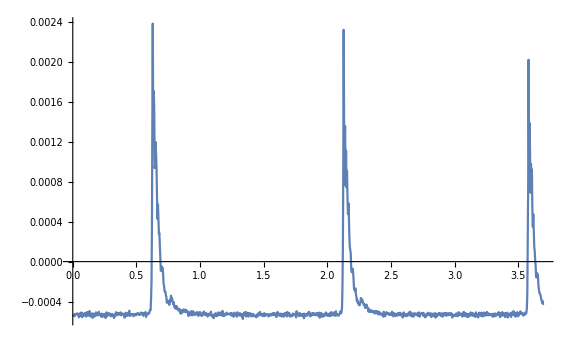

```mathematica
Show[%328,ImageSize->Large]
```

Import Directory of Data

```mathematica
directory="/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/DataAnalysis/mathematicaAnalysis";fileList=Import[directory];
SetDirectory[directory];
```

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/DataAnalysis/mathematicaAnalysis not found during Import.

SetDirectory::cdir: Cannot set current directory to /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/DataAnalysis/mathematicaAnalysis.

```mathematica
LaserDriftPlotTest[driftCSV_]:= Module[{driftData=driftCSV},
file=Import[driftData,{"Data",All,{1,3}}];

ListLinePlot[Drop[file,{1,3}]
,AxesLabel->Take[file,{4}]]]
Map[LaserDriftPlot,data]
```

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[LaserDriftPlot[$Failed],LaserDriftPlot[{1,3}]].

Drop[LaserDriftPlot[$Failed],LaserDriftPlot[{1,3}]]

```mathematica
filedata=Import["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trail3.csv",{"Data",Part[9;;],{1,3}}]
```

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trail3.csv not found during Import.

$Failed

```mathematica
Trial7=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial7.csv","Trial 7",Blue]
```

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial7.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,3}].

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,3}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial 7},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}]

```mathematica
Show[Trial7, PlotRange->{{0,1500},{-0.020,0.02}},ImageSize->Large,PlotLabel->"LaserDrift"]
```

Show::gtype: ListPlot is not a type of graphics.

Show[ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial 7},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],PlotRange→{{0,1500},{-0.02,0.02}},ImageSize→Large,PlotLabel→LaserDrift]